```mathematica
Clear[Lx, Ly, A, l1, l2, mL,
 SX2DDis, SX2DPDis,
 SY2DDis, SY2DPDis,
 CX2DDis, CX2DPDis,
 CY2DDis, CY2DPDis,
 Cons]
```

```mathematica
Lx = 28;
Ly =28;
l1 = 7;
l2 = 14;
mL = 14;
A = Lx*Ly + l2
```

798

```mathematica
(*-----------------------------------------------*)
```

```mathematica
SX2DDis=Table[0,{a,1,A},{b,1,A}];
Do[Do[{SX2DDis[[a + b Lx, a + 1 + b Lx]]=I/2, SX2DDis[[a + 1 + b Lx, a + b Lx]] = -I/2},{a,1, Lx -1}],{b,0, l1-1}]
Do[Do[{SX2DDis[[a + b(Lx+1)+ l1 Lx, a + 1 + b(Lx+1)+l1 Lx]]=I/2, SX2DDis[[a + 1 + b(Lx +1)+l1 Lx, a + b(Lx + 1) + l1 Lx]]= - I/2},{a,1,Lx}],{b,0,l2 -1}]
Do[Do[{SX2DDis[[a + b Lx + Lx(l1 + l2) + l2, a + b Lx + Lx(l1 + l2) + l2 + 1]]=I/2, SX2DDis[[a + b Lx + Lx(l1 + l2) + l2 + 1, a + b Lx + Lx(l1 + l2) + l2 ]]=-I/2},{a,1,Lx-1}],{b,0,Ly - (l1 + l2) -1}]
```

```mathematica
(*-----------------------------------------------*)
```

```mathematica
CX2DDis=Table[0,{a,1,A},{b,1,A}];
Do[Do[{CX2DDis[[a + b Lx, a + 1 + b Lx]]=1/2, CX2DDis[[a + 1 + b Lx, a + b Lx]] = 1/2},{a,1, Lx -1}],{b,0, l1-1}]
Do[Do[{CX2DDis[[a + b(Lx+1)+ l1 Lx, a + 1 + b(Lx+1)+l1 Lx]]=1/2, CX2DDis[[a + 1 + b(Lx +1)+l1 Lx, a + b(Lx + 1) + l1 Lx]]= 1/2},{a,1,Lx}],{b,0,l2 -1}]
Do[Do[{CX2DDis[[a + b Lx + Lx(l1 + l2) + l2, a + b Lx + Lx(l1 + l2) + l2 + 1]]=1/2, CX2DDis[[a + b Lx + Lx(l1 + l2) + l2 + 1, a + b Lx + Lx(l1 + l2) + l2 ]]=1/2},{a,1,Lx-1}],{b,0,Ly - (l1 + l2) -1}]
```

```mathematica
(*-----------------------------------------------*)
```

```mathematica
(**--Periodic in x--**)
```

```mathematica
SX2DPDis=Table[0,{a,1,A},{b,1,A}];
Do[{SX2DPDis[[(b+1)Lx,b Lx + 1]]=I/2,SX2DPDis[[b Lx + 1,(b+1) Lx ]]=-I/2},{b,0, l1-1}]
Do[{SX2DPDis[[(b+1)(Lx + 1)+l1 Lx, b(Lx + 1)+l1 Lx+1]]=I/2,SX2DPDis[[b(Lx + 1)+l1 Lx+1,(b+1)(Lx + 1)+l1 Lx]]=-I/2},{b,0, l2-1}]
Do[{SX2DPDis[[(b+1) Lx + Lx(l1 + l2) + l2, b Lx + 1 + Lx(l1 + l2) + l2]]=I/2, SX2DPDis[[b Lx + 1 + Lx(l1 + l2) + l2, (b+1) Lx + Lx(l1 + l2) + l2]]=-I/2},{b,0,Ly-(l1+l2)-1}]
```

```mathematica
(*-----------------------------------------------*)
```

```mathematica
CX2DPDis=Table[0,{a,1,A},{b,1,A}];
Do[{CX2DPDis[[(b+1)Lx,b Lx + 1]]=1/2,CX2DPDis[[b Lx + 1,(b+1) Lx ]]=1/2},{b,0, l1-1}]
Do[{CX2DPDis[[(b+1)(Lx + 1)+l1 Lx, b(Lx + 1)+l1 Lx+1]]=1/2,CX2DPDis[[b(Lx + 1)+l1 Lx+1,(b+1)(Lx + 1)+l1 Lx]]=1/2},{b,0, l2-1}]
Do[{CX2DPDis[[(b+1) Lx + Lx(l1 + l2) + l2, b Lx + 1 + Lx(l1 + l2) + l2]]=1/2, CX2DPDis[[b Lx + 1 + Lx(l1 + l2) + l2, (b+1) Lx + Lx(l1 + l2) + l2]]=1/2},{b,0,Ly-(l1+l2)-1}]
```

```mathematica
(*-----------------------------------------------*)
```

```mathematica
SY2DDis=Table[0,{a,1,A},{b,1,A}];
Do[Do[{SY2DDis[[a + b Lx, a + (b+1)Lx]]=I/2,SY2DDis[[a + (b+1) Lx, a + b Lx]]=-I/2},{a,1,Lx}],{b,0,l1-2}]
Do[Do[{SY2DDis[[a + b(Lx + 1) + l1 Lx, a + (b+1)(Lx + 1)+l1 Lx]]=I/2,SY2DDis[[a + (b+1)(Lx + 1) + l1 Lx, a + b(Lx + 1)+l1 Lx]]=-I/2},{a,1, Lx + 1}],{b,0,l2 -2}]
Do[Do[{SY2DDis[[a + b Lx + Lx (l1 + l2) + l2, a + (b+1)Lx + Lx (l1 + l2) + l2]]= I/2, SY2DDis[[a + (b+1)Lx + Lx (l1 + l2) + l2, a + b Lx + Lx (l1 + l2) + l2]] = -I/2},{a ,1,Lx}],{b,0, Ly - (l1 + l2) - 2}]
Do[{SY2DDis[[a + (l1-1) Lx, a + l1 Lx]]=I/2, SY2DDis[[a + l1 Lx, a + (l1-1)Lx]]=-I/2},{a,1,mL}]
Do[{SY2DDis[[a + mL + (l1-1)Lx, a + mL + 1+ l1 Lx]]=I/2, SY2DDis[[a + mL + 1+ l1 Lx, a + mL + (l1-1)Lx]]=-I/2},{a,1,Lx-mL}]
Do[{SY2DDis[[a+(l1 + l2)Lx+l2-(Lx+1), a + (l1 + l2)Lx + l2]]=I/2, SY2DDis[[a + (l1 + l2)Lx + l2, a + (l1+l2)Lx + l2-(Lx +1)]]=-I/2},{a,1,mL}]
Do[{SY2DDis[[a + (mL + 1) + (l1 + l2) Lx + l2 - (Lx+1), a + mL + (l1 + l2)Lx + l2]]=I/2, SY2DDis[[a + mL + (l1 + l2)Lx + l2, a + (mL + 1) + (l1 + l2) Lx + l2 - (Lx + 1)]]=-I/2},{a,1,Lx-mL}]
```

```mathematica
(*-----------------------------------------------*)
```

```mathematica
CY2DDis=Table[0,{a,1,A},{b,1,A}];
Do[Do[{CY2DDis[[a + b Lx, a + (b+1)Lx]]=1/2,CY2DDis[[a + (b+1) Lx, a + b Lx]]=1/2},{a,1,Lx}],{b,0,l1-2}]
Do[Do[{CY2DDis[[a + b(Lx + 1) + l1 Lx, a + (b+1)(Lx + 1)+l1 Lx]]=1/2,CY2DDis[[a + (b+1)(Lx + 1) + l1 Lx, a + b(Lx + 1)+l1 Lx]]=1/2},{a,1, Lx + 1}],{b,0,l2 -2}]
Do[Do[{CY2DDis[[a + b Lx + Lx (l1 + l2) + l2, a + (b+1)Lx + Lx (l1 + l2) + l2]]= 1/2, CY2DDis[[a + (b+1)Lx + Lx (l1 + l2) + l2, a + b Lx + Lx (l1 + l2) + l2]] = 1/2},{a ,1,Lx}],{b,0, Ly - (l1 + l2) - 2}]
Do[{CY2DDis[[a + (l1-1) Lx, a + l1 Lx]]=1/2, CY2DDis[[a + l1 Lx, a + (l1-1)Lx]]=1/2},{a,1,mL}]
Do[{CY2DDis[[a + mL + (l1-1)Lx, a + mL + 1+ l1 Lx]]=1/2, CY2DDis[[a + mL + 1+ l1 Lx, a + mL + (l1-1)Lx]]=1/2},{a,1,Lx-mL}]
Do[{CY2DDis[[a+(l1 + l2)Lx+l2-(Lx+1), a + (l1 + l2)Lx + l2]]=1/2, CY2DDis[[a + (l1 + l2)Lx + l2, a + (l1+l2)Lx + l2-(Lx +1)]]=1/2},{a,1,mL}]
Do[{CY2DDis[[a + (mL + 1) + (l1 + l2) Lx + l2 - (Lx+1), a + mL + (l1 + l2)Lx + l2]]=1/2, CY2DDis[[a + mL + (l1 + l2)Lx + l2, a + (mL + 1) + (l1 + l2) Lx + l2 - (Lx + 1)]]=1/2},{a,1,Lx-mL}]
```

```mathematica
(**---------------Periodic in y-----------------**)
```

```mathematica
SY2DPDis=Table[0,{a,1,A},{b,1,A}];
Do[{SY2DPDis[[Lx (Ly-1)+l2+a,a]]=I/2, SY2DPDis[[a, Lx(Ly-1)+l2+a]]=-I/2},{a,1,Lx}]
```

```mathematica
(*-----------------------------------------------*)
```

```mathematica
CY2DPDis=Table[0,{a,1,A},{b,1,A}];
Do[{CY2DPDis[[Lx (Ly-1)+l2+a,a]]=1/2, CY2DPDis[[a, Lx(Ly-1)+l2+a]]=1/2},{a,1,Lx}]
```

```mathematica
(*-----------------------------------------------*)
```

```mathematica
Cons=Table[0,{a,1,A},{b,1,A}];
Do[Cons[[a,a]]=1,{a,1,A}]
```

```mathematica
(*----------------------------------------------------------------------------------------------------------*)
(*----------------------------------------------------------------------------------------------------------*)
```

```mathematica
Clear[σ0,σ1,σ2,σ3,HamiltonianQAHI]
```

```mathematica
σ0=PauliMatrix[0];
σ1=PauliMatrix[1];
σ2=PauliMatrix[2];
σ3=PauliMatrix[3];
```

```mathematica
HamiltonianQAHI[t_,t0_,m_,α_]:=t*(KroneckerProduct[SX2DDis+α*SX2DPDis,σ1]+KroneckerProduct[SY2DDis+α*SY2DPDis, σ2])+KroneckerProduct[-m*Cons+t0*(CX2DDis+CY2DDis+α*CX2DPDis+α*CY2DPDis),σ3]
```

```mathematica
Clear[val,vec,ValVecAHI,ValAHI,ValAHIRange]
```

```mathematica
(*--------------------------------------------------------------------------------------------------------------------------------*)
```

```mathematica
Clear[val,vec,ValVecAHI,ValAHI,ValAHIRange]
```

```mathematica
{val,vec}=Eigensystem[HamiltonianQAHI[1.0,1.0,-1.0,1.0]];
```

```mathematica
ValVecAHI=SortBy[Transpose[{val,vec}],First];
```

```mathematica
ValAHI=Table[{j,Re[ValVecAHI[[j,1]]]},{j,1,2A}];
```

```mathematica
ValAHIRange=Table[ValAHI[[j,2]],{j,1,2 A}];
```

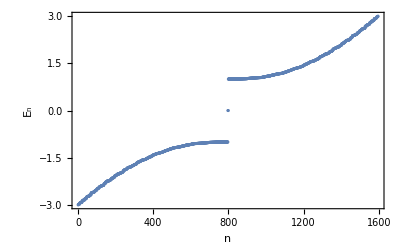

```mathematica
Show[ListPlot[ValAHI,Frame-> True,Axes-> False,PlotRange-> {{0,2A},{Min[ValAHIRange],Max[ValAHIRange]}}],(*Plot[0,{x,0,2A},PlotStyle-> Red],*)BaseStyle-> 14,FrameStyle-> Black,FrameLabel-> {"n","E_n"}]
```

```mathematica
Clear[Xaxis, Yaxis1, Yaxis2, Yaxis3, P3, P4, P2B]
```

```mathematica
Xaxis=Table[{{1,j},{Lx+1,j}},{j,1,Ly,1}];
```

```mathematica
Dimensions[Xaxis]
```

{28,2,2}

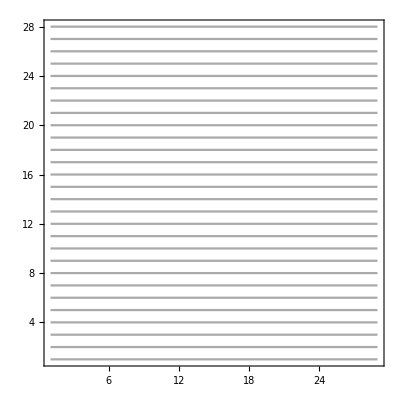

```mathematica
P3=Graphics[ListPlot[Table[Xaxis[[j]],{j,1,Ly}],Joined-> True,PlotStyle-> {{Lighter[Gray]}},PlotRange->{{1,Lx+1},{1,Ly}},Frame-> True,Axes-> False,AspectRatio->1],
FrameStyle->{{Black,Thick},{Black,Thick},{Black,Thick},{Black,Thick}},
FrameTicks-> {{{1,8,21,28},None},{{1,28/2,29},None}},BaseStyle-> 18]
```

```mathematica
Yaxis1=Table[{{j,1},{j,Ly}},{j,1,mL,1}];
```

```mathematica
Yaxis2={{mL+1,l1+1},{mL+1,l1+l2}};
```

```mathematica
Yaxis3=Table[{{j,1},{j,Ly}},{j,mL+2,Lx+1,1}];
```

```mathematica
Dimensions[Yaxis3]
```

{14,2,2}

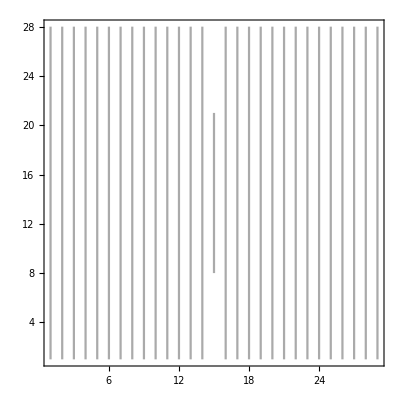

```mathematica
P4=Show[ListPlot[Table[Yaxis1[[j]],{j,1,mL}],Joined-> True,PlotStyle-> {{Lighter[Gray]}},PlotRange->{{1,Lx+1},{1,Ly}},Frame-> True,Axes-> False,AspectRatio->1],
ListPlot[Yaxis2,Joined-> True,PlotStyle-> Lighter[Gray]],
ListPlot[Table[Yaxis3[[j]],{j,1,Lx-mL}],Joined-> True,PlotStyle-> {{Lighter[Gray]}}]
]
```

```mathematica
(*------------------------------------------------------------------------------------------------------------------------------------------*)
```

```mathematica
(*------------------------------------------------------------------------------------------------------------------------------------------*)
```

```mathematica
P2B=Show[Graphics[{},

Frame->True,
FrameStyle->{{Black,Thick},{Black,Thick},{Black,Thick},{Black,Thick}},
FrameTicks-> {{{1,8,21,Ly},None},{{1,Lx/2+1,Lx+1},None}},BaseStyle-> 18,
PlotRange-> {{1,Lx+1},{1,Ly}}
]]
```

-Graphics-

```mathematica
(*------------------------------------------------------------------------------------------------------------------------------------------------------*)
```

```mathematica
(*------------------------------------------------------------------------------------------------------------------------------------------------------*)
```

```mathematica
(*------------------------------------------------------------------------------------------------------------------------------------------------------*)
```

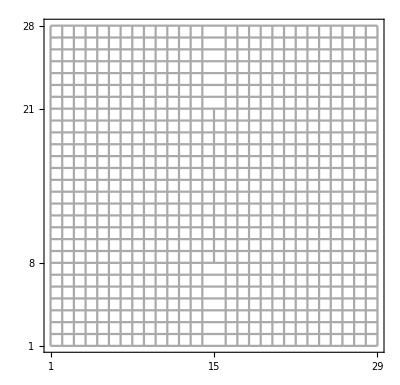

```mathematica
Show[P2B,P3,P4]
```